# Week 12

## Sunday 2/6:

Graphics - Bloch sphere (spin)

Ψ=a↑+b↓=cos(θ/2)e^(-iϕ/2)↑ + sin(θ/2)e^(+iϕ/2)↓ - Spin presentation , |a|^2+|b|^2=1
ρ= ∑^i  Pi|Ψi> <Ψi| , <O>=tr(ρO) , O is a general operator, Pi are the probabilities for Ψi.

```mathematica
DirectProduct[M1_,M2_]:=ArrayFlatten[Outer[Times,M1,M2]]
Kron[V1_,V2_]:=Flatten[Outer[Times,V1,V2]]
KetBra[V1_,V2_]:=Outer[Times,V1,Conjugate[V2]]
```

```mathematica
ρ={{ρ11,ρ12},{ρ21,ρ22}};
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
Ex=Tr[σx.ρ]
Ey=Tr[σy.ρ]
Ez=Tr[σz.ρ]
```

ρ12+ρ21

ⅈ ρ12-ⅈ ρ21

-ρ22+Ρ1⟦200,1⟧

```mathematica
R=1;Ω=1;δ0=10;
hamd={{δ,Ω },{Ω ,-δ}};(* Definition of Hamiltonian *)
resd=Eigensystem[hamd];

ham={{R t,Ω },{Ω,- R t}};(* Definition of Hamiltonian *)
Vec={up[t],down[t]};

eqs = Table[(ham.Vec)[[k]]==I D[Vec[[k]],t],{k,1,2}];
initial={up[-δ0/R]==-1,down[-δ0/R]==0};
sol=NDSolve[Join[eqs,initial],Vec,{t,-δ0/R,δ0/R},MaxSteps->10^7];
ρ1=KetBra[Vec,Vec]/.sol;
Ρ1=Table[ρ1/.t->δt ,{δt,-10,10,0.1}];
```

```mathematica
bloch1=Table[ρ11=Ρ1[[k,1]];{ρ11[[1,2]]+ρ11[[2,1]],I ρ11[[1,2]]-I ρ11[[2,1]],ρ11[[1,1]]-ρ11[[2,2]]}//Chop,{k,1,200,1}];
tbloch1=Transpose[bloch1];
```

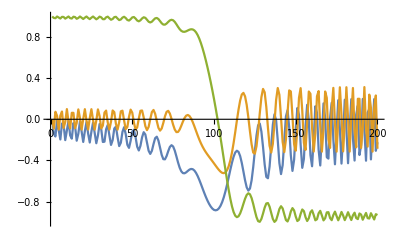

-Graphics3D-

-Graphics3D-

```mathematica
time1=Table[t,{t,-10,10,0.1}];
ListPlot[{tbloch1[[1]],tbloch1[[2]],tbloch1[[3]]},Joined->True]
ListPlot3D[bloch1]
ListPointPlot3D[bloch1]
```

Getting to know some Graphics:

```mathematica
Graphics3D[{Pink,Opacity[0.6],Specularity[1],Sphere[{0,0,0},0.7],Opacity[1],
Arrowheads[.03],Arrow[{{0,-1.2,0},{0,1.2,0}}],
Arrow[{{0,0,-1.2},{0,0,1.2}}],
Arrow[{{-1.2,0,0},{1.2,0,0}}],Text[Style[Row[{xSimNameGraph}],20,Bold,Purple], {0,0,1.45}],
Text[Style[Row[{"ρ_22-ρ_11"}], 16,Bold], {0,0,1.25}],
Text[Style[Row[{"Im(ρ_12)"}], 16,Bold], {0,1.28,-0.1}],
Text[Style[Row[{"Re(ρ_12)"}], 16,Bold], {1.28,0,-0.1}]},Boxed->False]
```

-Graphics3D-

```mathematica
sphaericLines=ParametricPlot3D[{{Cos[t], Sin[t],0},{0, Cos[t], Sin[t]},{ Cos[t],0,Sin[t]}},{t,0,2 π},PlotStyle->{{Black,Thin},{Black,Thin},{Black,Thin}},Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Graphics3D[{Opacity[0.15],Green,Arrowheads[.05],Arrow[Tube[{{0,0,0},{6,1,3}},0.02]]}]
```

-Graphics3D-

## Tuesday 4/6:

More Graphics:

```mathematica
axesVideo=
Graphics3D[{Black,Opacity[0.2],Specularity[1],Sphere[{0,0,0}],Opacity[1],
Arrowheads[.03],Arrow[{{0,-1.2,0},{0,1.2,0}}],
Arrow[{{0,0,-1.2},{0,0,1.2}}],
Arrow[{{-1.2,0,0},{1.2,0,0}}],Text[Style[Row[{xSimNameGraph}],8/5 24,Bold], {0,0,1.4}],
Text[Style[Row[{"ρ_22-ρ_11"}],8/5 16,Bold], {0,0,1.25}],
Text[Style[Row[{"Im(ρ_12)"}],8/5 16,Bold], {0,1.28,-0.1}],
Text[Style[Row[{"Re(ρ_12)"}],8/5 16,Bold], {1.28,0,-0.1}]},Boxed->False]
```

-Graphics3D-

```mathematica
sphaericLines=ParametricPlot3D[{{Cos[t], Sin[t],0},{0, Cos[t], Sin[t]},{ Cos[t],0,Sin[t]}},{t,0,2π},PlotStyle->{{Black,Thin},{Black,Thin},{Black,Thin}},Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Graphics3D[{Opacity[0.4],Brown,Arrowheads[.05],Arrow[Tube[{{0,0,0},{1,1,1}},0.02]]}]
```

-Graphics3D-

```mathematica
Graphics3D[{Green,Arrowheads[.05],Arrow[Tube[{{0,0,0},{1,1,1}},0.02]]}]
```

-Graphics3D-

f[[#]]&/@- inserts into the symbol # the list that comes after @ (mapping ), & ( a symbol for a function) Examples:

```mathematica
a=(#)&/@Range[1,5]
```

{1,2,3,4,5}

```mathematica
(#^2)&/@ {10,40,3,6}
```

{100,1600,9,36}

```mathematica
bloch=Interpolation[{time1[[#]],bloch1[[#]]}&/@Range[1,Length[bloch1]]];
```